# Bessel Functions. J_ν(x),Y_ν(x)

```mathematica
BesselJ[0, 0]
```

1

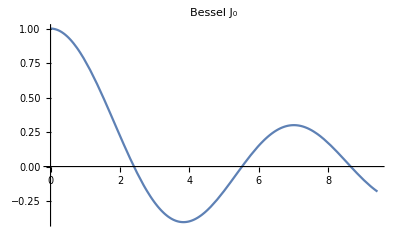
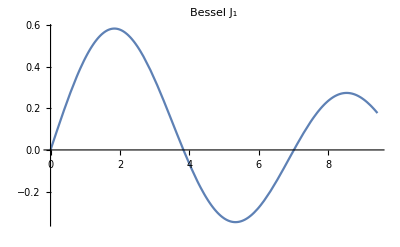
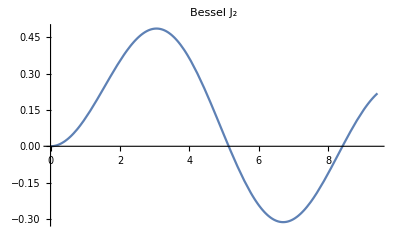
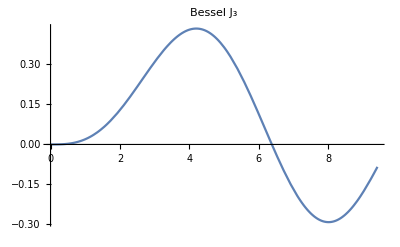
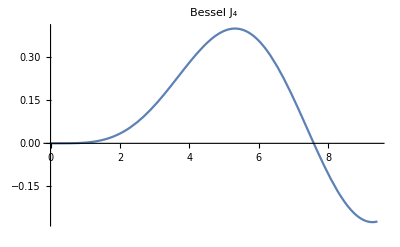

```mathematica
Table[Plot[BesselJ[ν,x], {x, 0, 3Pi},PlotLabel->"Bessel" Subscript[J, ν], PlotStyle-> , PlotLegends->Automatic], {ν, 0, 4}]
```

{BesselJ[0,x],BesselJ[1,x],BesselJ[2,x],BesselJ[3,x],BesselJ[4,x]}

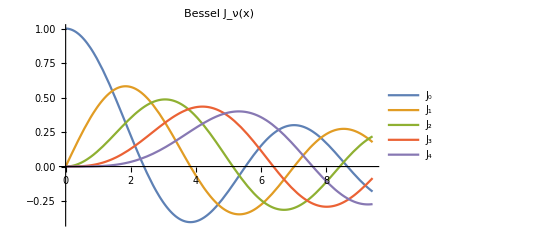

```mathematica
FewBesselJs = Table[BesselJ[ν, x], {ν, 0, 4}]
Plot[FewBesselJs, {x, 0, 3Pi}, PlotLabel->"Bessel J_ν(x)",PlotLegends->{Table[Subscript[J, ν], {ν, 0, 4}]}]
```

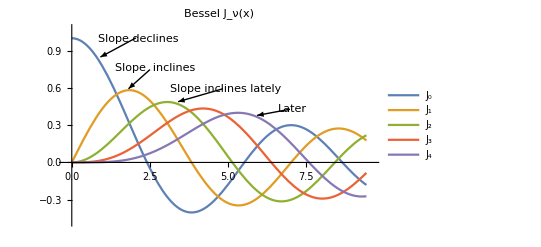

```mathematica
BesselJ[1, x]
BesselJ[-1, x]
```

BesselJ[1,x]

-BesselJ[1,x]

```mathematica
BesselY[0,0]
```

-∞

```mathematica
BesselY[0,1.]
```

0.088257

```mathematica
BesselY[1, 1.]
```

-0.781213

```mathematica
FewBesselYs = Table[BesselY[ν, x], {ν,0, 4}]
```

{BesselY[0,x],BesselY[1,x],BesselY[2,x],BesselY[3,x],BesselY[4,x]}

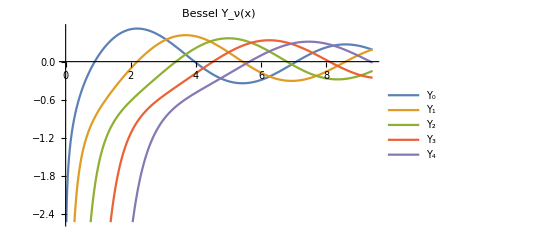

```mathematica
Plot[FewBesselYs, {x, 0., 3Pi}, PlotLabel->"Bessel Y_ν(x)",PlotLegends->{Table[Subscript[Y, ν], {ν, 0, 4}]}]
```

```mathematica
Plot[FewBesselYs,{x,0.,3 π},PlotTheme->"Detailed",PlotLabel->"Bessel \!\(\*SubscriptBox[StyleBox[\"Y\",FontSlant->\"Italic\"], \"ν\"]\)(x)",PlotLegends->{{Subscript[Y, 0],Subscript[Y, 1],Subscript[Y, 2],Subscript[Y, 3],Subscript[Y, 4]}}]
```

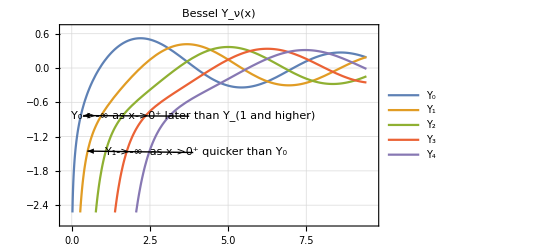

```mathematica
BesselY[1, x]
BesselY[-1, x]
```

BesselY[1,x]

-BesselY[1,x]

## Orthogonality of J_ν(x)and Y_ν(x)

Bessel J_ν is orthogonal with respect to the weight function = x on [0, R], where R is given and fixed boundary at which J_ν(kR)=0, where k is the scaling factor and has many values as the bessel function has many zeros.

(∫_0)^R  x J_ν(k_(n, m)x) J_ν(k_(n, j)x)dx = 0 for j != m, = (R^2/2) [J_(ν+1)(k_(n, m)R)]^2 for j =m

Finding root of Bessel J_0(x):

```mathematica
FindRoot[BesselJ[0,x], {x,0.1}]
```

{x→11.7915}

```mathematica
Plot[{BesselJ[0, 2.4048x], BesselJ[0, 11.79153x]}, {x, 0, 4Pi}, PlotRange->Full]
```

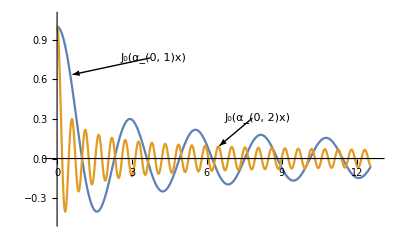

It is evident that the Bessel J_0(x) which is compressed horizontally by a lower zero oscillates slower than itself being compressed horizontally by a higher zero, in the same x range [-1, 1], i.e. the interval of orthogonality of the Legendre polynomials.

## Fourier-Legendre Series

Objectives:

To obtain Fourier constants in Fourier-Legendre Series of the function Bessel J_0(α_(0, 1)x), J_0(α_(0, 2)x)

To obtain m^th partial sum of the FL series of the above functions and plot it 5 values of m and compare which requires higher partial sums for coinciding with the og functions.

0.962548-1.05346 x^2

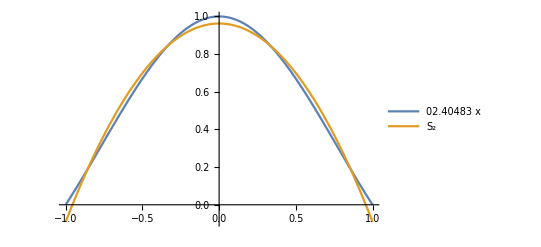

```mathematica
Subscript[α, 0, 1] = 2.404825557695773;
f[x_] :=BesselJ[0, Subscript[α, 0, 1]*x]
a[m_]:= (2m+1)/2 *Integrate[f[x]*LegendreP[m, x], {x, -1, 1}]
FLMthPartialSum=∑_(m=0)^2 a[m]*LegendreP[m, x] //Simplify
Plot[{f[x], FLMthPartialSum}, {x, -1, 1}, PlotLegends->{f[x],Subscript[S,2]}]
```

Bessel J_0(x) compressed horizontally by a smaller zero requires only 2^nd partial sum to give a good fit.

0.887175-25.084 x^2+163.946 x^4-405.034 x^6+421.85 x^8-156.861 x^10

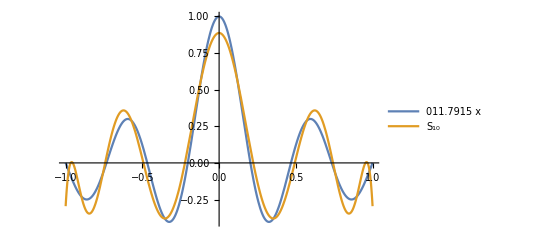

```mathematica
Subscript[α, 0, 2] = 11.791534439014281;
f[x_] :=BesselJ[0, Subscript[α, 0, 2]*x]
a[m_]:= (2m+1)/2 *Integrate[f[x]*LegendreP[m, x], {x, -1, 1}]
FLMthPartialSum=∑_(m=0)^10 a[m]*LegendreP[m, x] //Simplify
Plot[{f[x], FLMthPartialSum}, {x, -1, 1}, PlotLegends->{f[x],Subscript[S,10]}]
```

However, the Bessel J_0(x) compressed horizontally by a larger zero, as here, requires only 10^th partial sum to give a good fit., in the interval of orthogonality of the legendre polynomials.

Hence, the good fit index of the FL Series of compressed Bessels J_0(x) increases as a larger compressing factors, i.e. zeros of the J_0(x), are chose. In short, more oscillations conferred by more compression require more terms and thus a higher partial sum to practically coincide with the og function.